## Kapitola 10 - Síť RBF a Iris data

Demonstrace použití RBF sítě na datech z databáze UCI.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\BP

A načteme data.

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Předzpravování dat provedeme pomocí stejného postupu, který je popsán v kapitole 5 - Dopředná síť a Iris data.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, rozdělenou na vstupní a výstupní data, počet neuronů, případně můžeme zadat i aktivační funkci neuronu. Počet neuronů se zadává jako kladné celé číslo.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeRBFNet[inData,outData,4,Neuron->Sigmoid]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 23, 0, 31, 1.230015}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-5-23 at 0:31. The network has 4 inputs and 3 outputs.  It consists of 4 basis functions of Sigmoid type. The network has a linear submodel.

Natrénujeme síť pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("inData" a "outData") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení - obě tyto návratové hodnoty si ukládáme (do proměnné "net2" a "record").

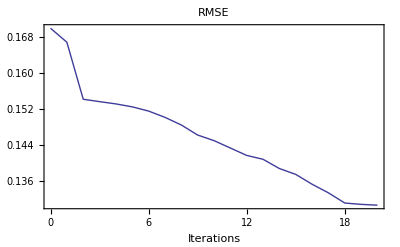

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Máme síť naučenou a můžeme se podívat na to, jak odpovídala během učení. Síť má 3 výstupy, proto následující příkaz vyprodukuje 3 grafy. Kadždý graf ukazuje počet správně a špatně klasifikovaných dat dané třídy v průběhu učení.

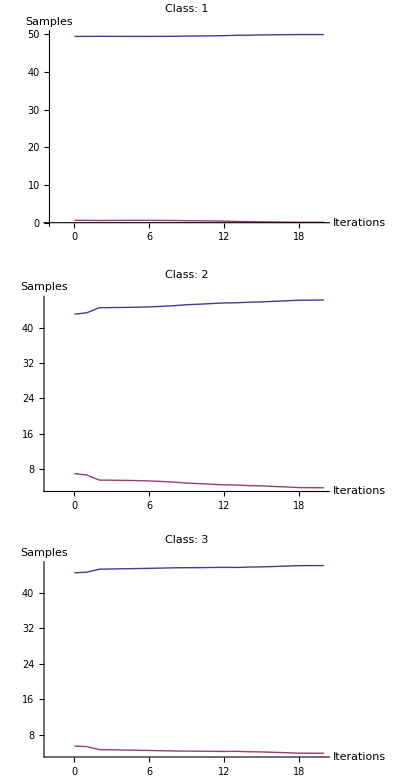

```mathematica
NetPlot[record,inData,outData,DataFormat->ClassPerformance]
```

Můžeme se podívat na klasifikaci pomocí "data/model" diagramu. Graf je interaktivní - pomocí myši ho můzeme otáčet, posouvat (Shift + myš) a zoomovat (Ctrl + myš). Čím víšší hodnoty jsou na diagonále, tím vyšší je úspěšnost klasifikace.

```mathematica
NetPlot[net2,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

Síť je možné si nechat symbolicky vyhodnotit - pro větší sítě je to ale už zcela nepřehledné, nicméně aktivační funkce tam zcela jistě poznáte.

Síť funguje v Mathematice jako klasická funkce, takže ji můžeme dávat parametry - včetně symbolů.

```mathematica
net2[{x1,x2,x3,x4}]
```

{1.99266+15.1068/(1+ⅇ^(0.0971394 (-6.78163+x1)^2+0.0971394 (-2.95348+x2)^2+0.0971394 (-3.57257+x3)^2+0.0971394 (-2.50002+x4)^2))-16.0859/(1+ⅇ^(0.12748 (-5.87704+x1)^2+0.12748 (-2.78839+x2)^2+0.12748 (-4.62212+x3)^2+0.12748 (-1.96525+x4)^2))+2.57865/(1+ⅇ^(0.37472 (-5.71108+x1)^2+0.37472 (-2.7526+x2)^2+0.37472 (-5.35046+x3)^2+0.37472 (-1.58289+x4)^2))-0.549714/(1+ⅇ^(0.751278 (-6.26069+x1)^2+0.751278 (-3.20722+x2)^2+0.751278 (-4.76204+x3)^2+0.751278 (-0.530066+x4)^2))-0.499497 x1-0.0312294 x2+0.433139 x3-0.347379 x4,-1.13228-22.7775/(1+ⅇ^(0.0971394 (-6.78163+x1)^2+0.0971394 (-2.95348+x2)^2+0.0971394 (-3.57257+x3)^2+0.0971394 (-2.50002+x4)^2))+25.4697/(1+ⅇ^(0.12748 (-5.87704+x1)^2+0.12748 (-2.78839+x2)^2+0.12748 (-4.62212+x3)^2+0.12748 (-1.96525+x4)^2))-6.51487/(1+ⅇ^(0.37472 (-5.71108+x1)^2+0.37472 (-2.7526+x2)^2+0.37472 (-5.35046+x3)^2+0.37472 (-1.58289+x4)^2))+3.73049/(1+ⅇ^(0.751278 (-6.26069+x1)^2+0.751278 (-3.20722+x2)^2+0.751278 (-4.76204+x3)^2+0.751278 (-0.530066+x4)^2))+0.669871 x1+0.101667 x2-0.841274 x3+0.409786 x4,0.13962+7.6707/(1+ⅇ^(0.0971394 (-6.78163+x1)^2+0.0971394 (-2.95348+x2)^2+0.0971394 (-3.57257+x3)^2+0.0971394 (-2.50002+x4)^2))-9.38387/(1+ⅇ^(0.12748 (-5.87704+x1)^2+0.12748 (-2.78839+x2)^2+0.12748 (-4.62212+x3)^2+0.12748 (-1.96525+x4)^2))+3.93623/(1+ⅇ^(0.37472 (-5.71108+x1)^2+0.37472 (-2.7526+x2)^2+0.37472 (-5.35046+x3)^2+0.37472 (-1.58289+x4)^2))-3.18078/(1+ⅇ^(0.751278 (-6.26069+x1)^2+0.751278 (-3.20722+x2)^2+0.751278 (-4.76204+x3)^2+0.751278 (-0.530066+x4)^2))-0.170374 x1-0.070438 x2+0.408135 x3-0.0624069 x4}

V následující kapitole se podíváme podrobněji na metody učení sítě.

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.